## Parameter Extraction for EGL-19 Voltage Gated Calcium Channel

```mathematica
AppendTo[$Path, "~/git/openworm_base/ion_channel_fitting"];
```

```mathematica
<<IonChannelFitter`
```

```mathematica
EGL19Series = Import["~/git/openworm_base/ion_channel_fitting/EGL-19_patch_clamp.csv"];
```

```mathematica
ionChannelParameterFit[series]
```

General::munfl: 0.304653 4.369958915974×10^-314 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.136] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1072.92] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

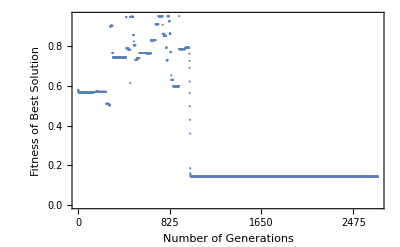
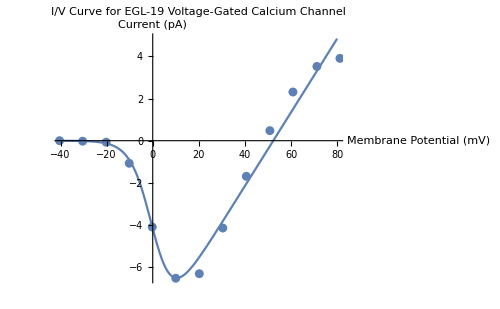
Number of Rounds:  | 2699
Total # of Solutions Explored:  | 272498
Norm of Top Solution  | 0.14299
Simulation History:  | -Graphics-
IV Curve:  | -Graphics-
Parameter Values:  | Gmax | 0.174637
Vh | 0.809287
k | 4.58897
Vrev | 52.2911

```mathematica
displayResults[$norms]
```